```mathematica
dados3 = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/FC - Projetos/P2/1a/Kutta_1a_3w0.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00990001},{2,0.02,0.999803,-0.0196001},{3,0.03,0.999559,-0.0291005},7992,{7996,79.96,-0.0592611,-0.0485318},{7997,79.97,-0.0597197,-0.0431773},{7998,79.98,-0.0601245,-0.0377839},{7999,79.99,-0.0604753,-0.0323565}}
 |  |  |  |

```mathematica
xt3 = dados3[[All, {2,3}]]
```

{{0,1},{0.01,0.99995},{0.02,0.999803},{0.03,0.999559},{0.04,0.999221},{0.05,0.998792},{0.06,0.998272},7986,{79.93,-0.0575673},{79.94,-0.0581844},{79.95,-0.0587492},{79.96,-0.0592611},{79.97,-0.0597197},{79.98,-0.0601245},{79.99,-0.0604753}}
 |  |  |  |

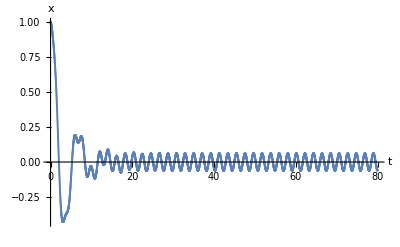

```mathematica
figxt3 = ListPlot[xt3, PlotRange->All, AxesLabel->{"t", "x"}]
```

```mathematica
vt3 = dados3[[All, {2,4}]]
```

{{0,0},{0.01,-0.00990001},{0.02,-0.0196001},{0.03,-0.0291005},{0.04,-0.0384016},{0.05,-0.047504},{0.06,-0.0564083},7986,{79.93,-0.0643143},{79.94,-0.0591051},{79.95,-0.0538427},{79.96,-0.0485318},{79.97,-0.0431773},{79.98,-0.0377839},{79.99,-0.0323565}}
 |  |  |  |

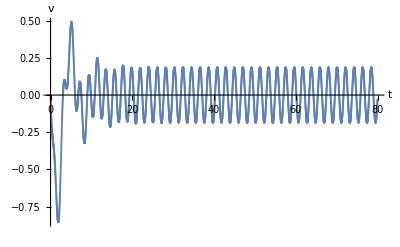

```mathematica
figvt3 = ListPlot[vt3, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
vx3 = dados3[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00990001},{0.999803,-0.0196001},{0.999559,-0.0291005},{0.999221,-0.0384016},{0.998792,-0.047504},7988,{-0.0581844,-0.0591051},{-0.0587492,-0.0538427},{-0.0592611,-0.0485318},{-0.0597197,-0.0431773},{-0.0601245,-0.0377839},{-0.0604753,-0.0323565}}
 |  |  |  |

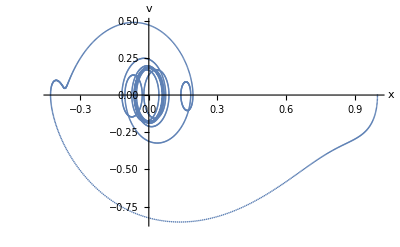

```mathematica
figvx3 =ListPlot[vx3, PlotRange->All, AxesLabel->{"x", "v"}]
```

```mathematica
dados2 = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/FC - Projetos/P2/1a/Kutta_1a_w0.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00994992},{2,0.02,0.999801,-0.0197993},{3,0.03,0.999555,-0.0295478},{4,0.04,0.999211,-0.0391949},7991,{7996,79.96,0.150044,-0.988679},{7997,79.97,0.14015,-0.99013},{7998,79.98,0.130242,-0.991482},{7999,79.99,0.12032,-0.992735}}
 |  |  |  |

{{0,1},{0.01,0.99995},{0.02,0.999801},{0.03,0.999555},{0.04,0.999211},{0.05,0.998771},{0.06,0.998236},{0.07,0.997608},7984,{79.92,0.189461},{79.93,0.179632},{79.94,0.169786},{79.95,0.159923},{79.96,0.150044},{79.97,0.14015},{79.98,0.130242},{79.99,0.12032}}
 |  |  |  |

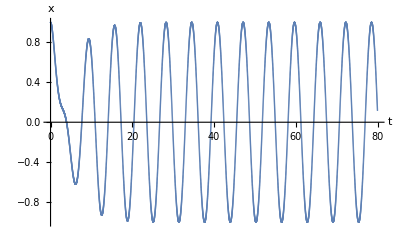

```mathematica
xt2 = dados2[[All, {2,3}]]
figxt2 = ListPlot[xt2, PlotRange->All, AxesLabel->{"t", "x"}]
```

{{0,0},{0.01,-0.00994992},{0.02,-0.0197993},{0.03,-0.0295478},{0.04,-0.0391949},{0.05,-0.04874},{0.06,-0.0581829},7986,{79.93,-0.983734},{79.94,-0.985481},{79.95,-0.987129},{79.96,-0.988679},{79.97,-0.99013},{79.98,-0.991482},{79.99,-0.992735}}
 |  |  |  |

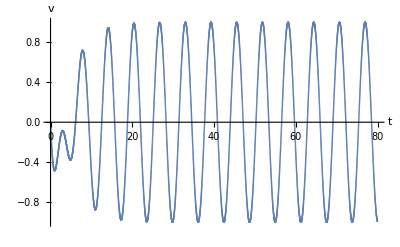

```mathematica
vt2 = dados2[[All, {2,4}]]
figvt2 = ListPlot[vt2, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
vx2 = dados2[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00994992},{0.999801,-0.0197993},{0.999555,-0.0295478},{0.999211,-0.0391949},{0.998771,-0.04874},7988,{0.169786,-0.985481},{0.159923,-0.987129},{0.150044,-0.988679},{0.14015,-0.99013},{0.130242,-0.991482},{0.12032,-0.992735}}
 |  |  |  |

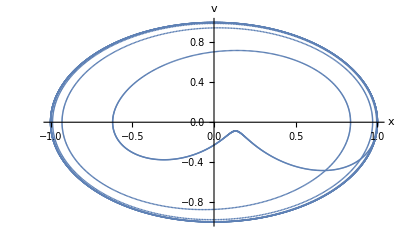

```mathematica
figvx2 =ListPlot[vx2, PlotRange->All, AxesLabel->{"x", "v"}]
```

```mathematica
dados1 = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/FC - Projetos/P2/1a/Kutta_1a_w0_3.dat",  "Table"]
```

{{0,0,1,0},{1,0.01,0.99995,-0.00996656},{2,0.02,0.999801,-0.0198658},{3,0.03,0.999553,-0.029697},{4,0.04,0.999207,-0.0394597},7991,{7996,79.96,0.537599,0.0430092},{7997,79.97,0.538026,0.0424117},{7998,79.98,0.538447,0.0418136},{7999,79.99,0.538862,0.0412151}}
 |  |  |  |

{{0,1},{0.01,0.99995},{0.02,0.999801},{0.03,0.999553},{0.04,0.999207},{0.05,0.998764},{0.06,0.998224},{0.07,0.997589},7984,{79.92,0.53583},{79.93,0.536281},{79.94,0.536726},{79.95,0.537165},{79.96,0.537599},{79.97,0.538026},{79.98,0.538447},{79.99,0.538862}}
 |  |  |  |

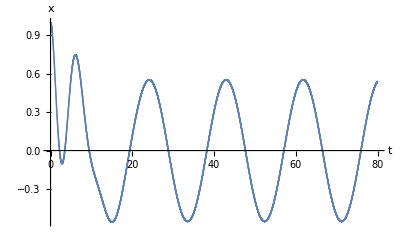

```mathematica
xt1 = dados1[[All, {2,3}]]
figxt1 = ListPlot[xt1, PlotRange->All, AxesLabel->{"t", "x"}]
```

{{0,0},{0.01,-0.00996656},{0.02,-0.0198658},{0.03,-0.029697},{0.04,-0.0394597},{0.05,-0.049153},{0.06,-0.0587766},7986,{79.93,0.0447991},{79.94,0.0442029},{79.95,0.0436063},{79.96,0.0430092},{79.97,0.0424117},{79.98,0.0418136},{79.99,0.0412151}}
 |  |  |  |

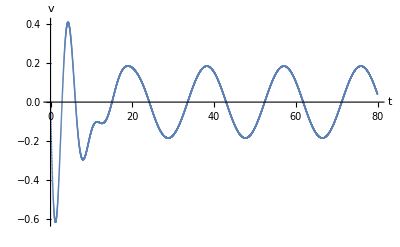

```mathematica
vt1 = dados1[[All, {2,4}]]
figvt1 = ListPlot[vt1, PlotRange->All, AxesLabel->{"t", "v"}]
```

```mathematica
vx1 = dados1[[All, {3,4}]]
```

{{1,0},{0.99995,-0.00996656},{0.999801,-0.0198658},{0.999553,-0.029697},{0.999207,-0.0394597},{0.998764,-0.049153},7988,{0.536726,0.0442029},{0.537165,0.0436063},{0.537599,0.0430092},{0.538026,0.0424117},{0.538447,0.0418136},{0.538862,0.0412151}}
 |  |  |  |

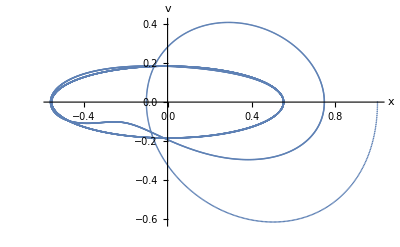

```mathematica
figvx1 =ListPlot[vx1, PlotRange->All, AxesLabel->{"x", "v"}]
```